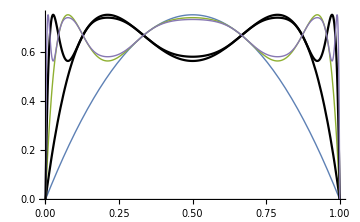

```mathematica
funcs=RecurrenceTable[{x[n+1]==r x[n] (1-x[n]),x[0]==x0},x,{n,1,5}];
Plot[funcs/.r->3,{x0,0,1},Evaluated->True,PlotRange->All]
```

This is an example from the Mathematica help pages.

```mathematica
k = 10; r = Range[3.,4.,1/(k-1)];
rhs[x_?VectorQ]:= r x(1 - x);
iterates = RecurrenceTable[{x[n+1]==rhs[x[n]],x[0]==ConstantArray[1./π,k]},x,{n, 10^4, 2 10^4}];//Timing
```

{0.276,Null}

```mathematica
data = Transpose[Ceiling[iterates k]];
count[data_, i_] := Module[{c, j},
{j, c} = Transpose[Tally[data]];
Transpose[{j, ConstantArray[i,Length[j]]}]->Log[N[c]]];
```

SparseArray[<49>, {10, 10}]

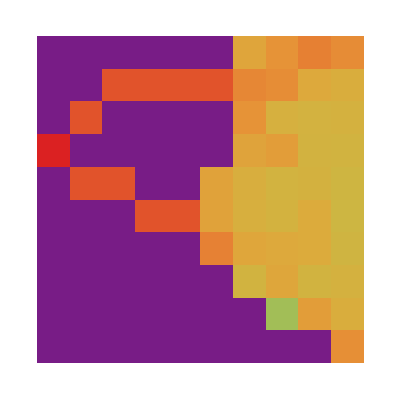

```mathematica
S = SparseArray[Table[count[data[[i]], i], {i, k}], k]
ArrayPlot[Reverse[S],ColorFunction->"Rainbow"]
```